## Analysis of Chromophore Organization in Various Light-Harvesting Complexes -- A Comparative Study

**  BE SURE TO SAVE OFTEN **
This program analyzes chromophore distributions of various photosynthetic complexes from the PDB. In investigating the correlations, the radial distribution functions, angle distribution, and interaction distributions are calculated.

To extract needed structural information, one first downloads the protein assembly data from the PDB. Then, use Chimera to construct repetitive structures and save the interested atom locations into .pdb file. Open VMD to read the file and save them into .xyz files. By using sed and awk operations, one can translate it into an Mathematica readable file.

The program tools are listed below as:
(i) General tools: raddf, angdf, coudf, lproj, etc.
(ii) Graphical tools: rdf, lambertplot, etc.
(iii) Quantitative tools: docomp, compos, sortdata, ds1, ds2, etc.

```mathematica
(* Load necessary libraries *)
Needs["VectorAnalysis`"]
```

```mathematica
(* i. General tools *)
const=300000;
coup[i_,j_]:=const 1/Norm[r[[i]]-r[[j]]]^3 (p[[i]].p[[j]]-3 (p[[i]].Normalize[r[[i]]-r[[j]]]) (p[[j]].Normalize[r[[i]]-r[[j]]]));
(* define the radial distribution function *)
(* This function is defined to calculate the pair distance distribution *)
raddf[data_]:=Flatten[j=2;Flatten[Delete[Reap[While[j<Length[data]+1,
Do[{t2={i=1;
Flatten[Delete[Reap[While[i<j,Do[{t1=Norm[data⟦i⟧-data⟦j⟧]},{1}];Sow[t1,a];i++];{a}],1],2]}},{1}];
Sow[t2,b];j++],{b}],1],2]]

(* define the angular distribution function *)
(* This will be done by constructing the distrubution of pair-pair vector dot-product *)
angdf[data_]:=Flatten[j=2;Flatten[Delete[Reap[While[j<Length[data]+1,
Do[{t2={i=1;
Flatten[Delete[Reap[While[i<j,Do[{t1=data⟦i⟧.data⟦j⟧},{1}];Sow[t1,a];i++];{a}],1],2]}},{1}];
Sow[t2,b];j++],{b}],1],2]] 

(* define the interaction distribution function *)
(* This will be done by constructing the distrubution of dipole-dipole interactions *)
coudf[data1_,data2_]:=Flatten@{r=data1;p=data2;Flatten[j=2;Flatten[Delete[Reap[While[j<Length[data1]+1,
Do[{t2={i=1;
Flatten[Delete[Reap[While[i<j,Do[{t1=coup[i,j]},{1}];Sow[t1,a];i++];{a}],1],2]}},{1}];
Sow[t2,b];j++],{b}],1],2]] }

(* Define the orientation matrix *)
(* Define the orientation matrix *)
matrixO[dataset_]:=({{Total[dataset⟦All,1⟧^2], Total[Times@@@dataset⟦All,{1,2}⟧], Total[Times@@@dataset⟦All,{1,3}⟧]}, {Total[Times@@@dataset⟦All,{1,2}⟧], Total[dataset⟦All,2⟧^2], Total[Times@@@dataset⟦All,{2,3}⟧]}, {Total[Times@@@dataset⟦All,{1,3}⟧], Total[Times@@@dataset⟦All,{2,3}⟧], Total[dataset⟦All,3⟧^2]}})

(* Define direction cosines *)
(* input: dataset in Cartesian coordinates *)
(* output: the three direction cosines*)
θ[dataset_]:=Table[CoordinatesFromCartesian[dataset⟦i⟧],{i,1,Length@dataset}]⟦All,2⟧
ϕ[dataset_]:=Table[CoordinatesFromCartesian[dataset⟦i⟧],{i,1,Length@dataset}]⟦All,3⟧
α[dataset_]:=(Sin/@θ[dataset])*(Cos/@ϕ[dataset])
β[dataset_]:=(Sin/@θ[dataset])*(Sin/@ϕ[dataset])
γ[dataset_]:=Cos/@θ[dataset]

(* ii. Graphical tools *)

rdf[dataset_,nbins_,plotlimit_]:=Module[{
res=Reap[Histogram[dataset,nbins,(Sow[{#1,#2}];#2)&]]},
bins=Union[Flatten[res[[2,1,1,1]]]];
counttemp=N[Mean/@res[[2,1,1,1]]]^2;
counts0=res[[2,1,1,2]]/counttemp;
counts=counts0/Total@counts0;
Histogram[dataset,{bins},counts&,PlotRange->{{0,plotlimit},Automatic},AxesOrigin->{0,0},AxesStyle->{{Medium},{Medium}},PlotLabel->"Radial Distribution Function: ",FormatType->StandardForm,(*AxesLabel->{"Chromophore Pair-Pair Distance (10^-1 nm)","Frequency (a.u.)"},*)AxesStyle->Thick]]

(* Example code for the Lambert map *)
(*
Show[{ListPlot[data,AxesStyle->Dashed,PlotRange->{{-2^0.5,2^0.5},{-2^0.5,2^0.5}},AspectRatio->1],
ListContourPlot[BinCounts[data,0.2*2^0.5,0.2*2^0.5],ContourShading->None,ContourStyle->Dashed,Contours->4,InterpolationOrder->3,PerformanceGoal->"Quality",DataRange->{{-2^0.5,2^0.5},{-2^0.5,2^0.5}},RegionFunction->Function[{x,y,z},Norm[{x,y}]<2^0.5],BoundaryStyle->Red]}]
*)


(* Below are methods inspired from the book, "Statistical Analysis of Spherical Data" *)

(* function for Lambert projection >> equal-area projection for statistical analysis of spherical data *)
(* Lambert's azimuthal equal-area projection has the property of axisymmetric distortion about the modal orientation. This projection maps the entire sphere to a disc, with the north pole in hte centre and the south pole distorted to a ring about the circumference. In order to avoid this severe distortion, one often trancate an half sphere and display the other hemisphere in an adjacent projection. *)

(* input: samples in 3d-rectangular coordinates *)
(* output: 2D projection vector map (ψ,ρ) *)
lproj[dataset_]:=Module[{datasetprime=Table[CoordinatesFromCartesian[dataset⟦i⟧,Spherical],{i,1,Length@dataset}]},If[0<=datasetprime⟦1,2⟧<=0.5π,{ρ=2Sin/@(0.5datasetprime⟦All,2⟧);ψ=datasetprime⟦All,3⟧;Partition[Riffle[ψ,ρ],2]},{ρ=2Sin/@(π/2-0.5datasetprime⟦All,2⟧);ψ=datasetprime⟦All,3⟧;Partition[Riffle[ψ,ρ],2]}]]
(* This sortdata function divides the directional data to two parts, ones direct upward, the other direct downward *)
sortdata[dataset_]:=Module[{datasetprime=Table[CoordinatesFromCartesian[dataset⟦i⟧,Spherical],{i,1,Length@dataset}]},FlattenAt[Reap[For[i=1,i<Length@datasetprime+1,i++,If[0<=datasetprime⟦All,2⟧⟦i⟧<=0.5π,Sow[i,upper],Sow[i,lower]]],{upper,lower}]⟦2⟧,{{1},{2}}]]

(* function for plotting Lambert map *)
(* 
usage WITHOUT sorting the data: 
ex=Lproj[dataset_]
Show[ListPolarPlot[ex],PolarPlot[2.^0.5,{t,0,2π},PlotStyle->Black]]
*)
lambertplot[dataset_]:={
upp=sortdata[dataset]⟦1⟧;
low=sortdata[dataset]⟦2⟧;
temp=lproj/@{dataset⟦upp⟧,dataset⟦low⟧};
Table[Show[ListPolarPlot[temp⟦i⟧],PolarPlot[2.^0.5,{t,0,2π},PlotStyle->Black]],{i,1,2}]}

(* iii. Quantitative tools *)
decomp[x_]:=Module[{xx=(Floor[(1+√(8x+1))/2]-1)(Floor[(1+√(8x+1))/2])/2},If[x-xx==0,{Floor[(1+√(8x+1))/2]-1,Floor[(1+√(8x+1))/2]},{x-xx,Floor[(1+√(8x+1))/2]+1}]]
compos[a_,b_]:=Module[{xx=((b-2)*(b-1))/2},xx+a]

(* Generate to-be-analysed datasets *)
(* dimers around RDF peaks *)
(* imput: mg locations, dipole orientations, peak location, peak width *)
(* ds1 extracts locations of the Chromophores with specific range, and then take their intersection *)
ds1[mgloc_,diploc_,mean_,sd_]:=
Module[{ds=Intersection@Flatten[j=2;Flatten[Delete[Reap[While[j<Length[mgloc]+1,
Do[{t2={i=1;
Flatten[Delete[Reap[While[i<j,Do[{t1=Norm[mgloc⟦i⟧,mgloc⟦j⟧]},{1}];If[mean-sd<t1<mean+sd,Sow[{i,j},a]];i++];{a}],1],2]}},{1}];
Sow[t2,b];j++],{b}],1],2]]},{diploc⟦ds⟧,ds}]

(* ds2 extracts locations of the Chromophores with specific range, but do not take their intersection *)
(* Usage:
ListPlot[Apply[Dot,ds2[mgloc,diploc,mean,sd]⟦1⟧,1]]
*)
ds2[mgloc_,diploc_,mean_,sd_]:=
Module[{ds=Flatten[j=2;Flatten[Delete[Reap[While[j<Length[mgloc]+1,
Do[{t2={i=1;
Flatten[Delete[Reap[While[i<j,Do[{t1=Norm[mgloc⟦i⟧-mgloc⟦j⟧]},{1}];If[mean-sd<t1<mean+sd,Sow[{i,j},a]];i++];{a}],1],2]}},{1}];
Sow[t2,b];j++],{b}],1],2],3]},{Table[diploc⟦ds⟦i⟧⟧,{i,1,Length@ds}],ds}]

(* ds3 extracts pair of the chromophores that are larger than certain coupling strength *)
(* usage:

*)

ds3[mgloc_,diploc_,cutoff_]:=
Reap[r=mgloc;p=diploc;
For[j=2,j<Length@r+1,j++,
For[i=1,i<j,i++,Which[coup[i,j]>cutoff,Sow[{i,j},plus],coup[i,j]<-cutoff,Sow[{i,j},minus]]
]],
{plus,minus}]





(* function to calculate the distance to the m-th nearest Chl. *)
(* input: data = mg-locatation data in cartesian coordinates *)
(* usage:
nearest[k,l];
k = the number of chrmophore from the mg-location data;
l = the diatance to the l-th nearest Chl.; note that nearest[k,0]=0 
*)
(*data=mg3PCQdata;
temp1=Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}];
Table[temp2[k]=Ordering[temp1⟦k⟧];,{k,1,Length@data}];
nearest[k_,l_]:=temp1⟦k⟧⟦temp2[k]⟧⟦l⟧*)
```

## LHCII (loaded)

2BHW (pea): Sample 不夠...

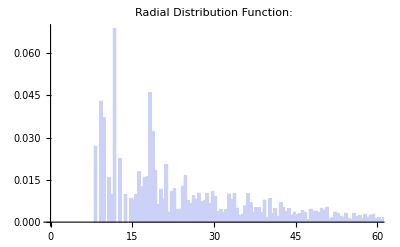

```mathematica
(* read Mg atomic locations from the PDB file *)
mg2BHWdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2BHW_MG"]];
mg2BHW=raddf[mg2BHWdata];
rdf[mg2BHW,500,60]

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2BHW_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2BHW_ND"]];
d2BHWdata=Normalize/@(nb-nd);
d2BHW=ArcCos/@angdf[d2BHWdata];
```

## LHCII (only MG loaded)

1RWT (Spinach): Sample 太大...

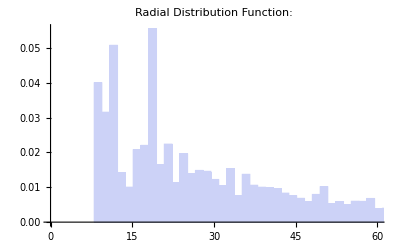

```mathematica
(* read Mg atomic locations from the PDB file *)
mg1RWTdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1RWT_MG"]];
mg1RWT=raddf[mg1RWTdata];
rdf[mg1RWT,500,60]

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1RWT_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1RWT_ND"]];
d1RWTdata=Normalize/@(nb-nd);
d1RWT=ArcCos/@angdf[d1RWTdata];
```

## 1JB0: Crystal Structure of Photosystem I: a Photosynthetic Reaction Center and Core Antenna System from Cyanobacteria

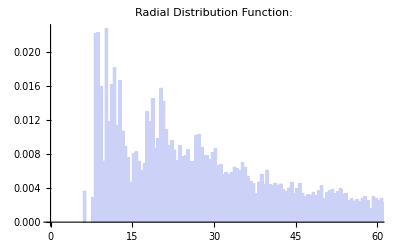

```mathematica
(* read Mg atomic locations from the PDB file *)
mg1JB0data=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_MG"]];
mg1JB0=raddf[mg1JB0data];
rdf[mg1JB0,500,60]

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/1JB0_ND"]];
d1JB0data=Normalize/@(nb-nd);
d1JB0=ArcCos/@angdf[d1JB0data];
```

```mathematica
(*Module[{name="1JB0"},ListPlot[Partition[Riffle[mg1JB0,d1JB0],2],PlotLabel->"Pair-Pair Distance-Angle Relation: "<>name,AxesLabel->{"Pair-Pair Distance","Pair-Pair Angle"}]]*)
```

## 3KZI: Crystal Structure of Monomeric Form of Cyanobacterial Photosystem II

## 3ARC: Crystal structure of oxygen-evolving Photosystem II at 1.9 angstrom resolution

```mathematica
(* There exists problem in the two datasets!! *)
```

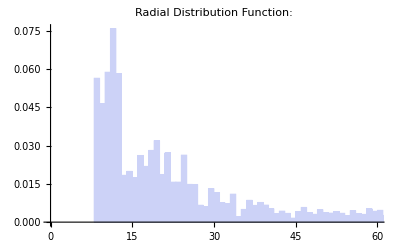

```mathematica
(* read Mg atomic locations from the PDB file *)
mg3ARCdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3ARC_MG"]];
mg3ARC=raddf[mg3ARCdata];
rdf[Select[mg3ARC,#>8.&],500,60]

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3ARC_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3ARC_ND"]];
d3ARCdata=Normalize/@(nb-nd);
d3ARC=ArcCos/@angdf[d3ARCdata];
```

## 2FKW: Structure of LH2 from Rps. acidophila crystallized in lipidic mesophases

```mathematica
(* read Mg atomic locations from the PDB file *)
mg2FKWdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2FKW_MG"]];
mg2FKW=raddf[mg2FKWdata];

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2FKW_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/2FKW_ND"]];
d2FKWdata=Normalize/@(nb-nd);
d2FKW=ArcCos/@angdf[d2FKWdata];
```

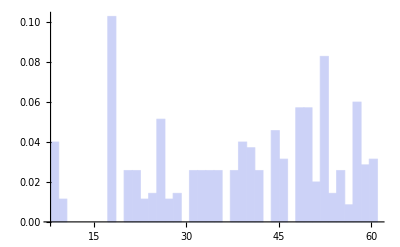

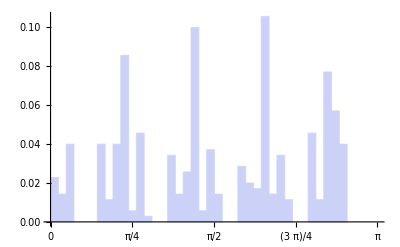

```mathematica
Histogram[mg2FKW,40,"Probability"]
Histogram[d2FKW,40,"Probability",PlotRange->{{0,π},Automatic},Ticks->{{0,π/4,π/2,(3π)/4,π},Automatic}]
```

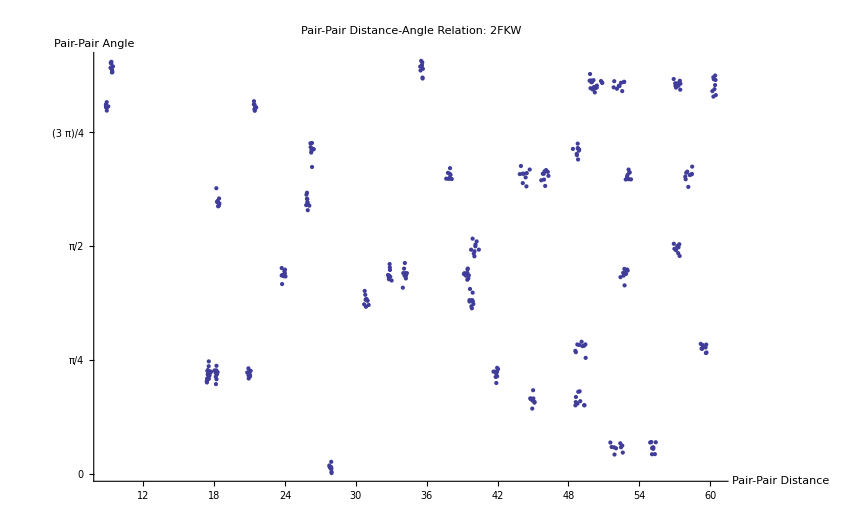

```mathematica
Module[{name="2FKW"},ListPlot[Partition[Riffle[mg2FKW,d2FKW],2],Ticks->{Automatic,{0,π/4,π/2,(3π)/4,π}},PlotLabel->"Pair-Pair Distance-Angle Relation: "<>name,AxesLabel->{"Pair-Pair Distance","Pair-Pair Angle"}]]
```

## 3PCQ : Photosystem I

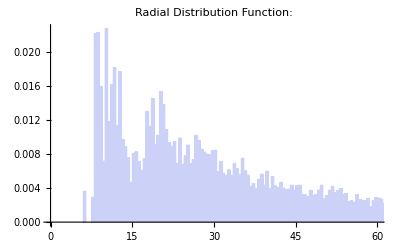

```mathematica
(* read Mg atomic locations from the PDB file *)
mg3PCQdata=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3PCQ_MG"]];
mg3PCQ=raddf[mg3PCQdata];
rdf[mg3PCQ,500,60]

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3PCQ_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3PCQ_ND"]];
d3PCQdata=Normalize/@(nb-nd);
d3PCQ=ArcCos/@angdf[d3PCQdata];
```

## 3LW5: Improved model of plant photosystem I

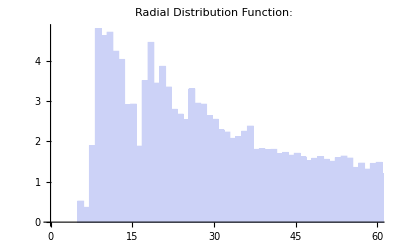

```mathematica
(* read Mg atomic locations from the PDB file *)
mg3LW5data=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3LW5_MG"]];
mg3LW5=raddf[mg3LW5data];
rdf[mg3LW5,500,60]

(* read NB and ND info from this PDB file *)
nb=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3LW5_NB"]];
nd=ToExpression[Import["~/Documents/Research/Arrangements_Mar.2010-/PDB\ files/3LW5_ND"]];
d3LW5data=Normalize/@(nb-nd);
d3LW5=ArcCos/@angdf[d3LW5data];
```

## old, unorganized stuff

```mathematica
data=mg3PCQdata;
```

```mathematica
knn[l_]:=knn[l]=Table[Ordering[Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}]⟦ii⟧]⟦{1,l}⟧,{ii,1,Length@data}]
```

```mathematica
knnmean[l_]:=Mean@(EuclideanDistance@@@Table[Part[data,knn[l]⟦i⟧],{i,1,Length[data]}])
knnacc[lll_]:=Mean[Flatten[Table[EuclideanDistance@@@Table[Part[data,knn[ll]⟦i⟧],{i,1,Length[data]}],{ll,2,lll}]]]
knnvar[l_]:=Variance@(EuclideanDistance@@@Table[Part[data,knn[l]⟦i⟧],{i,1,Length[data]}])
knnskew[l_]:=Skewness@(EuclideanDistance@@@Table[Part[data,knn[l]⟦i⟧],{i,1,Length[data]}])
knnskurt[l_]:=Kurtosis@(EuclideanDistance@@@Table[Part[data,knn[l]⟦i⟧],{i,1,Length[data]}])
```

```mathematica
Show[{DiscretePlot[knnmean[l],{l,2,40,1},PlotStyle->Red],DiscretePlot[knnacc[l],{l,2,40,1}]}]
```

$Aborted

```mathematica
Show[{DiscretePlot[knnmean[l],{l,2,40,1},PlotStyle->Red],DiscretePlot[knnacc[l],{l,2,40,1}]}]
```

$Aborted

```mathematica
ListPointPlot3D[Table[Part[data,list⟦i⟧],{i,1,Length[data]}]]
```

-Graphics3D-

```mathematica
Table[Length[Union[list⟦i⟧,list⟦j⟧]],{i,1,96},{j,1,96}]//MatrixForm
```

```mathematica
Graphics3D@Line[Table[Part[data,list⟦i⟧],{i,1,Length[data]}]]
```

```mathematica
Graphics3D[Line[Table[Part[data,list⟦i⟧],{i,1,Length[data]}]]]
```

-Graphics3D-

```mathematica
mgtest=raddf[Mean/@Table[Part[data,list⟦i⟧],{i,1,Length[data]}]];
```

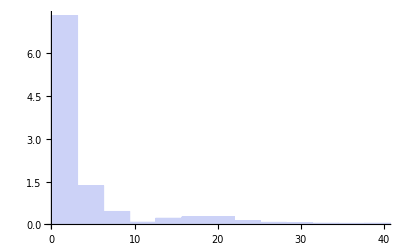

```mathematica
res=Reap[Histogram[mgtest,50,(Sow[{#1,#2}];#2)&]];
bins=Union[Flatten[res[[2,1,1,1]]]];
counts=res[[2,1,1,2]]/(Mean/@res[[2,1,1,1]])^2//N;
itpl=Interpolation[Partition[Riffle[Mean/@res[[2,1,1,1]],counts],2],InterpolationOrder->3];
Show[Histogram[mgtest,{bins},counts&,PlotRange->{{0,40},Automatic},AxesOrigin->{0,0}]]
```

```mathematica
knn[l_]:=knn[l]=Table[Ordering[Table[Norm[data⟦i⟧-data⟦j⟧],{i,1,Length[data]},{j,1,Length[data]}]⟦ii⟧]⟦{1,l}⟧,{ii,1,Length@data}]
```

```mathematica
r=mg1JB0data;
```

```mathematica
Length@r
```

96

```mathematica
p=.
```

```mathematica
p=d1JB0data;
```

```mathematica
coup[i_,j_]:=const 1/Norm[r[[i]]-r[[j]]]^3 (p[[i]].p[[j]]-3 (p[[i]].Normalize[r[[i]]-r[[j]]]) (p[[j]].Normalize[r[[i]]-r[[j]]]))
```

```mathematica
Table[If[i==j,0,coup[i,j]],{i,1,3},{j,1,3}]
```

{{0,-64.3014,45.6909},{-64.3014,0,-32.6159},{45.6909,-32.6159,0}}

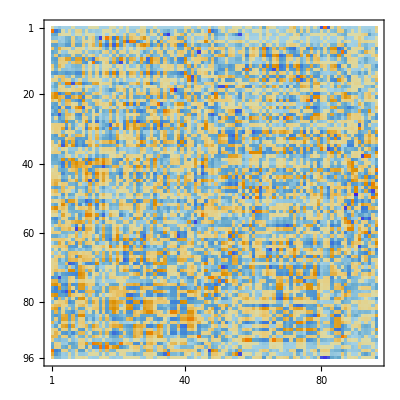

```mathematica
MatrixPlot@Eigenvectors[Table[If[i==j,12500.,coup[i,j]],{i,1,96},{j,1,96}]]
```

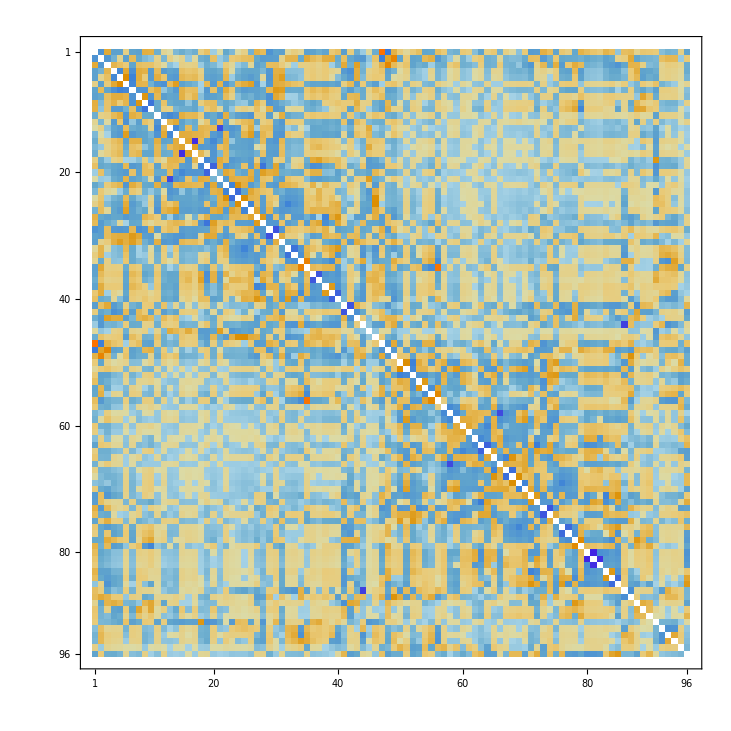

```mathematica
MatrixPlot[Table[If[i==j,0,coup[i,j]],{i,1,96},{j,1,96}]]
```

```mathematica
Table[If[i==j,0,coup[i,j]],{i,1,3},{j,1,3}]
```

{{0,-64.3014,45.6909},{-64.3014,0,-32.6159},{45.6909,-32.6159,0}}

```mathematica
Ordering/@Table[If[i==j,0,coup[i,j]],{i,1,3},{j,1,3}]
```

{{2,1,3},{1,3,2},{2,3,1}}

```mathematica
Length[p]
```

96

```mathematica
randomtab=.
```

```mathematica
p=.;pspherical=.;
```

```mathematica
pspherical:={1.,RandomReal[{0,π}],RandomReal[{-π,π}]}
```

```mathematica
randomps=Table[pspherical,{96}];
```

```mathematica
p=Table[CoordinatesToCartesian[randomps[[i]],Spherical],{i,1,96}];
```

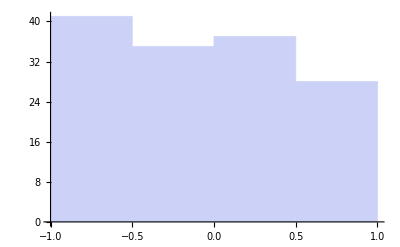

```mathematica
Histogram[Take[angdf[p],141],20]
```

```mathematica
normaltab=Table[If[i==j,0,coup[i,j]],{i,1,96},{j,1,96}];
```

```mathematica
randomtab:=Table[If[i==j,0,coup[i,j]],{i,1,96},{j,1,96}];
```

```mathematica
MatrixPlot[(normaltab-randomtab)]
```

$Aborted

```mathematica
r=mg1JB0data;p=d1JB0data;
Table[If[i==j,0,coup[i,j]],{i,1,4},{j,1,4}]
```

{{0,14.9617,6.19803,2.76142},{14.9617,0,-175.327,54.4289},{6.19803,-175.327,0,277.036},{2.76142,54.4289,277.036,0}}

```mathematica
Ordering/@%1369;
```

```mathematica
Table[{j,Table[%1374⟦i,1⟧,{i,1,96}]⟦j⟧},{j,1,96}];
```

```mathematica
Show[Graphics3D[{Red,Line[Table[Part[mg1JB0data,%1378⟦i⟧],{i,1,96}]]}],Graphics3D[{Blue,Line[Table[Part[mg1JB0data,%1377⟦i⟧],{i,1,96}]]}]]
```

-Graphics3D-

```mathematica
Table[{j,Table[%1374⟦i,96⟧,{i,1,96}]⟦j⟧},{j,1,96}];
```